bin = δ/B

```mathematica
n=5;center=2^(n-1);bin=0.3;noise=0.3;
```

```mathematica
yk[k_Integer]:=Module[{Ωkt},
If[k<0 ||k>=2^n,Print["Unexpected integer k"];Return[]];
Ωkt=π √(1+(k-center)^2 bin^2);
Sin[Ωkt/2] π/Ωkt+noise*RandomVariate[NormalDistribution[]]//N
]
```

```mathematica
xj[j_Integer]:=Module[{M},
If[j<0 ||j>=2^n,Print["Unexpected integer k"];Return[]];
M=2^n;
1/(√M)Sum[yk[k]Exp[-(2π I j k)/M],{k,0,M-1}]//Series[#,{λ,0,1}]&//Normal//N
]
```

```mathematica
jList=Table[j,{j,0,2^n-1}];
```

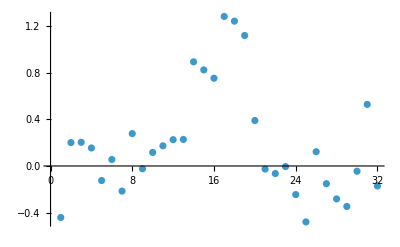

```mathematica
ListPlot[yk/@jList]
```

```mathematica
xList=xj[#]&/@jList;
```

```mathematica
xAbs=(#/Total[#]&[Abs[xList]])^2;
```

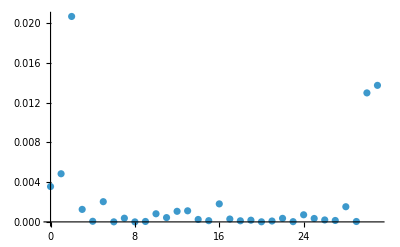

```mathematica
ListPlot[{jList,xAbs}//Transpose,PlotRange->All]
```